```mathematica
r = 0.7;
x0 = 1.5;
maxt = 20;
lista = NestList[r # (1-#)&,x0,maxt];
ListPlot[lista]
```

-Graphics-

0.7

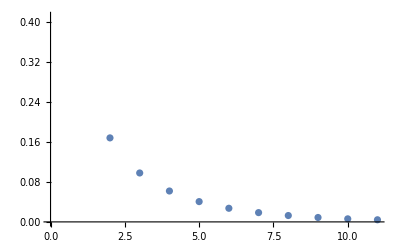

{29,44,22,11,17,26,13,20,10,5,8,4,2,1}

```mathematica
(*Dada f[x_] y r se crea la trayectoria xt*)
f[x_]:=r x (1-x)
r = 0.7

x0 = 0.6; tmax = 10;
lista = NestList[f,x0,tmax];
ListPlot[lista]
(*Se define el atractor como aquel tal que el error es menor a una tolerancia*)
FixedPointList[f,x0]

lista[[-1]]

(*Pruebo para distintas condiciones iniciales random*)
```